## Metric

metric:

ds^2= -a(r)dt^2+ dr^2/(b(r))+ r^2 dθ^2+ r^2 sin^2 θ dΩ^2  .

a(r) = b(r) = 1 - (2M)/r+ζ^2/r^2(1-(2M)/r)^2  .

## Lapce function

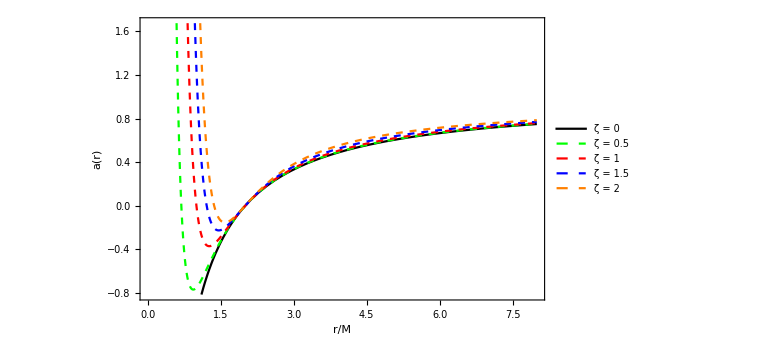

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Plot[{a[r,0],a[r,0.5],a[r,1],a[r,1.5],a[r,2]},{r,0,8},Frame->True,FrameLabel->{"r/M","a(r)"},ImageSize->Large,PlotStyle-> {{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue},{Dashed,Orange}},PlotLegends->Placed[{"ζ = 0","ζ = 0.5","ζ = 1","ζ = 1.5","ζ = 2"},{Scaled[{0.70,0.5}],{0.8,1.15}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```

### event horizon

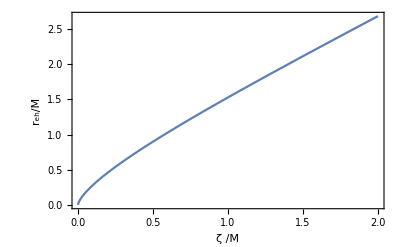

{{r→2},{r→-ζ^2/(3^(1/3) (9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))+((9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))/3^(2/3)},{r→((1+ⅈ √3) ζ^2)/(2 3^(1/3) (9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))-((1-ⅈ √3) (9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))/(2 3^(2/3))},{r→((1-ⅈ √3) ζ^2)/(2 3^(1/3) (9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))-((1+ⅈ √3) (9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))/(2 3^(2/3))}}

```mathematica
reh[ζ_] := ζ^2/(3^(1/3) (9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))+((9 ζ^2+√3 √(27 ζ^4+ζ^6))^(1/3))/3^(2/3)

Plot[reh[ζ],{ζ,0,2},Frame->True,FrameLabel->{"ζ /M","r_eh/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
Solve[a[r,ζ]==0,r]
```

## Effective Potential uchp

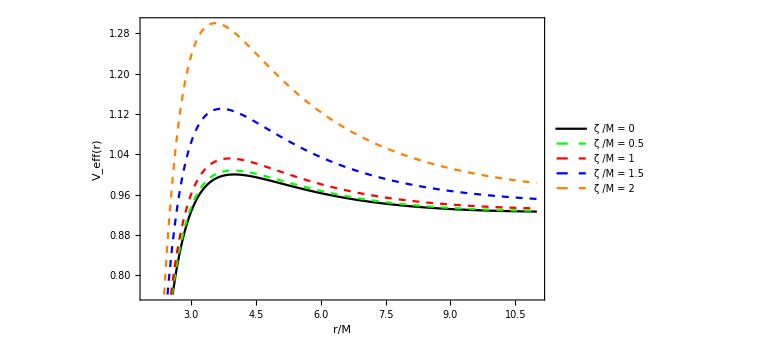

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Veff[L_,r_,ζ_] := a[r,ζ](1 + L^2/r^2)
veff[Ene_,L_,ζ_,r_] :=-1 - L^2/r^2- Ene^2/a[r,ζ]
Plot[{Veff[4,r,0],Veff[4,r,0.5],Veff[4,r,1],Veff[4,r,2],Veff[4,r,3]},{r,2,11},Frame->True,FrameLabel->{"r/M","V_eff(r)"," ℒ = 4"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue},{Dashed,Orange}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 0.5","ζ /M = 1","ζ /M = 1.5","ζ /M = 2"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large]
```

### angular momentum of particle

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 13 of {{L→-3.4641,r→6.},{L→3.4641,r→6.}} does not exist.

ReplaceAll::reps: {{{L→-3.4641,r→6.},{L→3.4641,r→6.}}⟦13⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

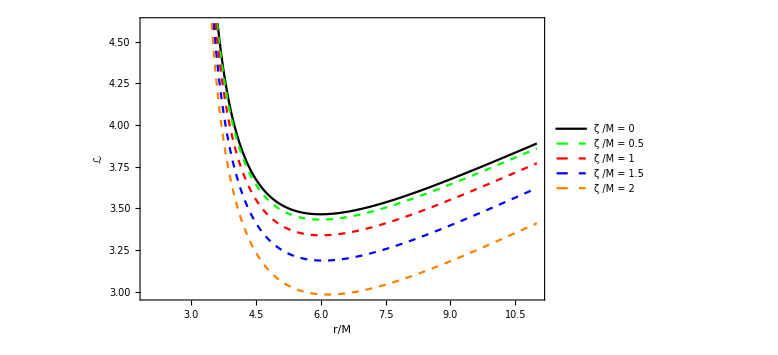

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
ris[ζ_]:=r/.Solve[D[Veff[L,r,ζ],r]==0&&D[Veff[L,r,ζ],r,r]==0,{L,r}][[13]]
L[ζ_,r_]=L/.Solve[D[Veff[L,r,ζ],r]==0,L][[2]];
Ene[ζ_,r_]:=(a[r,ζ] (1+ L[ζ,r]^2/r^2))^0.5
NSolve[D[L[0,r],r]==0,r];
ris[0.]//N;
Plot[{L[0,r],L[0.5,r],L[1,r],L[1.5,r],L[2,r]},{r,2,11},Frame->True,FrameLabel->{"r/M","ℒ"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue},{Dashed,Orange}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 0.5","ζ /M = 1","ζ /M = 1.5","ζ /M = 2"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large]
Plot[Ene[0,r],{r,0,5}];
(*Plot[ris[ζ],{ζ,0,4},Frame->True]*)
```

### energy of particle

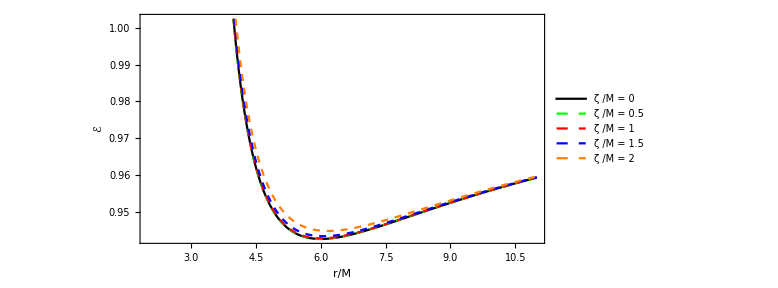

```mathematica
Ene[ζ_,r_]:=(a[r,ζ] (1+ L[ζ,r]^2/r^2))^0.5
Plot[{Ene[0,r],Ene[0.5,r],Ene[1,r],Ene[1.5,r],Ene[2,r]},{r,2,11},Frame->True,FrameLabel->{"r/M","ℰ"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red},{Dashed,Blue},{Dashed,Orange}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 0.5","ζ /M = 1","ζ /M = 1.5","ζ /M = 2"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large,AspectRatio->0.5]
```

### isco

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

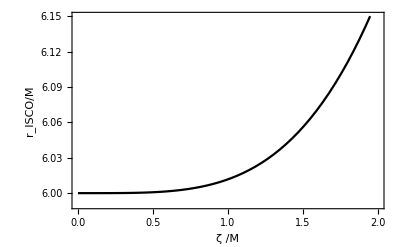

```mathematica
ris[ζ_]:=r/.Solve[D[Veff[L,r,ζ],r]==0&&D[Veff[L,r,ζ],r,r]==0,{L,r}][[13]]
Plot[ris[ζ],{ζ,0,2},PlotRange->{{0,2},{5.99,6.15}},Frame->True,FrameLabel->{"ζ /M","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->Black]
```

## Effective Potential chp

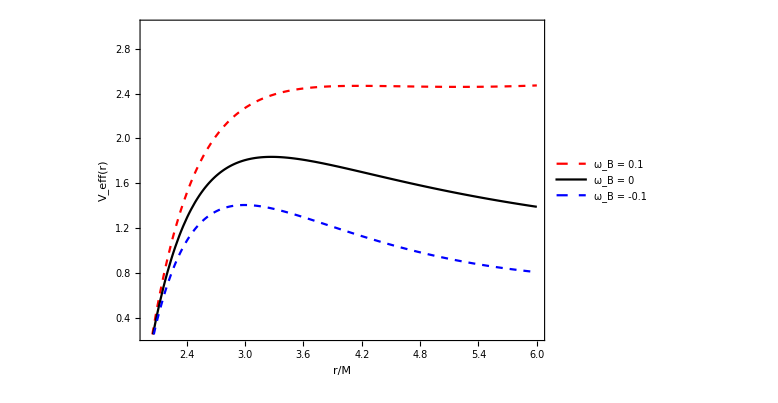

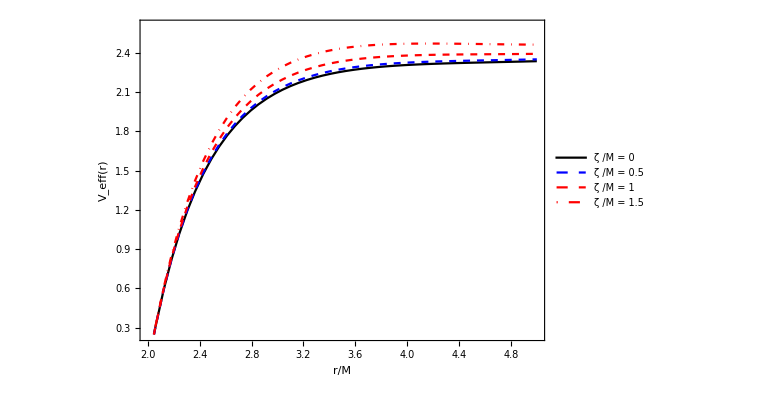

```mathematica
a[r_,ζ_] := 1- 2/r+ζ^2/r^2(1-2/r)^2
Veeff[L_,ω_,r_,ζ_] := a[r ,ζ] (1+(L/r+ ω r)^2)
Plot[{Veeff[6,0.1,r,1.5],Veeff[6,0,r,1.5],Veeff[6,-0.1,r,1.5]},{r,2,6},Frame->True,FrameLabel->{"r/M","V_eff(r)"," ℒ = 6,  ζ /M = 1.5,   ω_B = qB/(2  mc)"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Dashed,Red},{Black},{Dashed, Blue}},PlotLegends->Placed[{"ω_B = 0.1", "ω_B = 0","ω_B = -0.1"},{Scaled[{0.70,0.5}],{-0.2,-0.1}}],ImageSize->Large,AspectRatio->0.7, PlotRange->{{2.,6},{0.25,3}}]


Plot[{Veeff[6,0.1,r,0],Veeff[6,0.1,r,0.5],Veeff[6,0.1,r,1],Veeff[6,0.1,r,1.5]},{r,2,5},Frame->True,FrameLabel->{"r/M","V_eff(r)"," ℒ = 6, ω_B = 0.1"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Blue},{Dashed,Red},{DotDashed,Red}},PlotLegends->Placed[{"ζ /M = 0", "ζ /M = 0.5","ζ /M = 1","ζ /M = 1.5"},{Scaled[{0.70,0.5}],{-0.2,1.5}}],ImageSize->Large,AspectRatio->0.7,PlotRange->{{2.,5},{0.25,2.6}}]
```

### angular momentum

```mathematica
L[r_,ζ_,ω_] :=L/. Solve[D[a[r ,ζ] (1+(L/r+ ω r)^2),r]==0,{L,r}][[1]]
```

### isco radii dep on ω_B

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

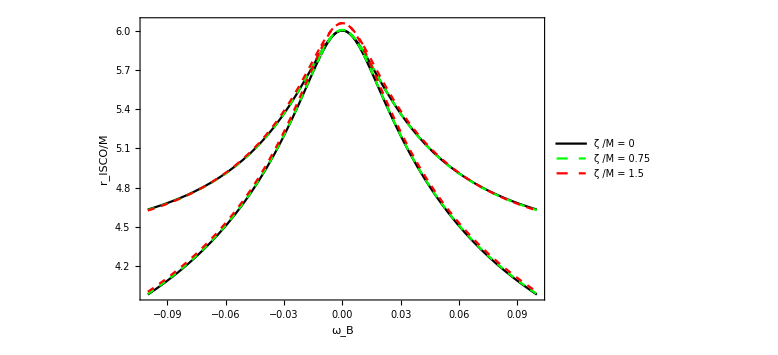

```mathematica
risc[ζ_,ω_] := r/.Solve[D[Veeff[L,ω,r,ζ],r]==0&&D[Veeff[L,ω,r,ζ],r,r]==0,{L,r}]
risc[0,0];


Plot[{risc[0,ω],risc[0.75,ω],risc[1.5,ω]},{ω,-0.1,0.1},Frame->True,FrameLabel->{"ω_B","r_ISCO/M"," ℒ = 4"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotStyle->{{Black},{Dashed,Green},{Dashed,Red}},PlotLegends->Placed[{"ζ /M = 0","ζ /M = 0.75","ζ /M = 1.5"},{Scaled[{0.70,0.5}],{-0.3,-0.1}}],ImageSize->Large]
```